```mathematica
w={1,1}
```

{1,1}

```mathematica
c=0.5
```

0.5

```mathematica
f[x_]=w.x+c
```

0.5+{1,1}.x

```mathematica
d=0.5
```

0.5

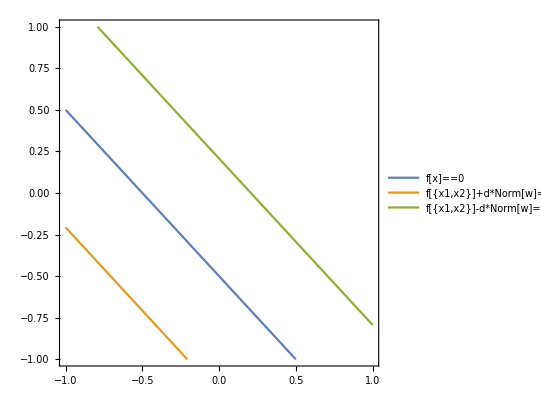

```mathematica
ContourPlot[{f[{x1,x2}]==0,f[{x1,x2}]+d*Norm[w]==0,f[{x1,x2}]-d*Norm[w]==0},{x1,-1,1},{x2,-1,1},PlotLegends->{"f[x]==0","f[{x1,x2}]+d*Norm[w]==0","f[{x1,x2}]-d*Norm[w]==0"}]
```